# Load the second-order punctures

## Load the punctures and rotate

The punctures in the in the rotated coordinated system where the particle is at the pole

```mathematica
Get[NotebookDirectory[]<>"h2Pilm.m"]
```

```mathematica
TraceReverse[i_]:=Switch[i,3,6,6,3,_,i]
```

```mathematica
ScalarVectorTensorMax[i_]:=Switch[i,1,2,2,2,3,2,4,3,5,3,6,2,7,4,8,3,9,3,10,4];
```

```mathematica
ScalarVectorTensorMaxSS[i_]:=Switch[i,1,2,2,3,3,2,4,3,5,3,6,2,7,4,8,3,9,3,10,4];
```

```mathematica
δr =-(r0^3/(3 M)) (r0-3M)/(r0-2M) Fr;
```

```mathematica
h2P["SS",i_Integer,l1_,m1_]:=h2P["SS",i,l1,m1]=Block[{hSS,l=l1,m=m1,ω,r},
	ω = m Ω;
	2π Sum[hSSlm[TraceReverse[i]][l,mp]WignerD[{l,m,mp},π,π/2,π/2]/.{r->Δr+r0,Abs[Δr]->Sqrt[Δr^2]},{mp,-Min[l,ScalarVectorTensorMaxSS[i]],Min[l,ScalarVectorTensorMaxSS[i]]}]/.Log[Δr]->1/2Log[Δr^2]
];


h2P["SR",i_Integer,l1_,m1_]:=h2P["SR",i,l1,m1]=Block[{hSS,l=l1,m=m1,ω,r},
	ω=m Ω;
	2π Sum[hSRlm[TraceReverse[i]][l,mp]WignerD[{l,m,mp},π,π/2,π/2]/.{r->Δr+r0,Abs[Δr]->Sqrt[Δr^2]},{mp,-Min[l,ScalarVectorTensorMax[i]],Min[l,ScalarVectorTensorMax[i]]}]
];


h2P["δm",i_Integer,l1_,m1_]:=h2P["δm",i,l1,m1]=Block[{l=l1,m=m1,ω,r},
	ω=m Ω;
	2π Sum[hδmlm[TraceReverse[i]][l,mp]WignerD[{l,m,mp},π,π/2,π/2]/.{r->Δr+r0,Abs[Δr]->Sqrt[Δr^2]},{mp,-Min[l1,ScalarVectorTensorMax[i]],Min[l1,ScalarVectorTensorMax[i]]}]
];

h2P["δz",i_Integer,l1_,m1_]:=h2P["δz",i,l1,m1]=Block[{hSS,l=l1,m=m1,ω,r},
	ω=m Ω;
	2π Sum[hδzlm[TraceReverse[i]][l,mp]WignerD[{l,m,mp},π,π/2,π/2]/.{r->Δr+r0,Abs[Δr]->Sqrt[Δr^2]},{mp,-Min[l1,ScalarVectorTensorMaxSS[i]],Min[l1,ScalarVectorTensorMaxSS[i]]}]
];

h2P["ms",i_Integer,l1_,m1_]:=h2P["ms",i,l1,m1]=Block[{l=l1,m=m1,ω,r},
	ω=m Ω;
	2π Sum[hmslm[TraceReverse[i]][l,mp]WignerD[{l,m,mp},π,π/2,π/2]/.{r->Δr+r0,Abs[Δr]->Sqrt[Δr^2]},{mp,-Min[l1,ScalarVectorTensorMax[i]],Min[l1,ScalarVectorTensorMax[i]]}]
];
```

### Extra pieces for the δm punctures

```mathematica
Clear[δm]
Evaluate[Table[δm[a,b],{a,1,4},{b,1,4}]]={{1/(3 r0^3) (-((24 M (2 M-r0) δr)/(1-(3 M)/r0))+3 r0^3 hR1[1,1]+(12 (2 M-r0) r0^2 (hR1[1,1]+Sqrt[M/r0^3] hR1[1,4]))/(1-(3 M)/r0)-r0 (-2 M+r0)^2 hR1[2,2]+(2 M-r0) hR1[3,3]+(2 M-r0) hR1[4,4]+(3 r0 (2 M r0-r0^2+(2 (-2 M+r0)^2)/(1-(3 M)/r0)) (hR1[1,1]+Sqrt[M/r0^3] (2 hR1[1,4]+Sqrt[M/r0^3] hR1[4,4])))/(1-(3 M)/r0)),2/3 hR1[1,2]+(2 (-1+(2 M)/r0) (hR1[1,2]+Sqrt[M/r0^3] hR1[2,4]))/(1-(3 M)/r0),2/3 hR1[1,3]+(2 (-1+(2 M)/r0) (hR1[1,3]+Sqrt[M/r0^3] hR1[3,4]))/(1-(3 M)/r0),(4 (M-r0) Sqrt[M/r0^3] δr)/(1-(3 M)/r0)+2/3 hR1[1,4]+(2 Sqrt[M/r0^3] r0^2 (hR1[1,1]+Sqrt[M/r0^3] hR1[1,4]))/(1-(3 M)/r0)+(2 (-1+(2 M)/r0) (hR1[1,4]+Sqrt[M/r0^3] hR1[4,4]))/(1-(3 M)/r0)+(2 (2 M-r0) Sqrt[M/r0^3] r0 (hR1[1,1]+Sqrt[M/r0^3] (2 hR1[1,4]+Sqrt[M/r0^3] hR1[4,4])))/(1-(3 M)/r0)^2},{2/3 hR1[1,2]+(2 (-1+(2 M)/r0) (hR1[1,2]+Sqrt[M/r0^3] hR1[2,4]))/(1-(3 M)/r0),1/3 (2 hR1[2,2]+((r0 hR1[1,1])/(2 M-r0)+hR1[2,2]-(2 M hR1[2,2])/r0+(hR1[3,3]+hR1[4,4])/r0^2)/(1-(2 M)/r0)-(3 r0 (hR1[1,1]+Sqrt[M/r0^3] (2 hR1[1,4]+Sqrt[M/r0^3] hR1[4,4])))/((1-(3 M)/r0) (2 M-r0))),2/3 hR1[2,3],2/3 hR1[2,4]+(2 Sqrt[M/r0^3] r0^2 (hR1[1,2]+Sqrt[M/r0^3] hR1[2,4]))/(1-(3 M)/r0)},{2/3 hR1[1,3]+(2 (-1+(2 M)/r0) (hR1[1,3]+Sqrt[M/r0^3] hR1[3,4]))/(1-(3 M)/r0),2/3 hR1[2,3],1/3 ((r0^3 hR1[1,1])/(2 M-r0)-2 M r0 hR1[2,2]+3 hR1[3,3]+hR1[4,4]+r0^2 (hR1[2,2]+(3 (hR1[1,1]+2 Sqrt[M/r0^3] hR1[1,4]+(M hR1[4,4])/r0^3))/(1-(3 M)/r0))),2/3 hR1[3,4]+(2 Sqrt[M/r0^3] r0^2 (hR1[1,3]+Sqrt[M/r0^3] hR1[3,4]))/(1-(3 M)/r0)},{(4 (M-r0) Sqrt[M/r0^3] δr)/(1-(3 M)/r0)+2/3 hR1[1,4]+(2 Sqrt[M/r0^3] r0^2 (hR1[1,1]+Sqrt[M/r0^3] hR1[1,4]))/(1-(3 M)/r0)+(2 (-1+(2 M)/r0) (hR1[1,4]+Sqrt[M/r0^3] hR1[4,4]))/(1-(3 M)/r0)+(2 (2 M-r0) Sqrt[M/r0^3] r0 (hR1[1,1]+Sqrt[M/r0^3] (2 hR1[1,4]+Sqrt[M/r0^3] hR1[4,4])))/(1-(3 M)/r0)^2,2/3 hR1[2,4]+(2 Sqrt[M/r0^3] r0^2 (hR1[1,2]+Sqrt[M/r0^3] hR1[2,4]))/(1-(3 M)/r0),2/3 hR1[3,4]+(2 Sqrt[M/r0^3] r0^2 (hR1[1,3]+Sqrt[M/r0^3] hR1[3,4]))/(1-(3 M)/r0),1/3 (r0^3 ((24 M δr)/((1-(3 M)/r0) r0^3)+hR1[1,1]/(2 M-r0))-2 M r0 hR1[2,2]+hR1[3,3]+3 hR1[4,4]+(6 M r0 (hR1[1,1]+Sqrt[M/r0^3] (2 hR1[1,4]+Sqrt[M/r0^3] hR1[4,4])))/(1-(3 M)/r0)^2+r0^2 (hR1[2,2]+(3 (hR1[1,1]+6 Sqrt[M/r0^3] hR1[1,4]+(5 M hR1[4,4])/r0^3))/(1-(3 M)/r0)))}};
Clear[δmdot]
Evaluate[Table[δmdot[a,b],{a,1,4},{b,1,4}]]={{(4 M (-2 M+r0) (-3 M r0^(3/2) hR1[1,2]+2 r0^(5/2) hR1[1,2]-6 M^(3/2) hR1[2,4]+3 Sqrt[M] r0 hR1[2,4]))/(3 r0^4 (-3 M+r0)^(3/2)),1/(3 r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0)) (-8 M^(3/2) r0^(5/2) hR1[1,4]+4 Sqrt[M r0^7] hR1[1,4]+24 M^4 r0 hR1[2,2]-8 M^3 (-9 r0 δr+4 r0^2 hR1[2,2]-3 hR1[4,4])+2 M r0^2 (6 r0 δr+r0^2 (2 hR1[1,1]-hR1[2,2])+3 hR1[4,4])-2 M^2 r0 (30 r0 δr+r0^2 (3 hR1[1,1]-7 hR1[2,2])+12 hR1[4,4])),-((2 M (-2 M+r0) hR1[2,3])/(3 r0^(5/2) Sqrt[-3 M+r0])),-((4 (-2 M+r0) (Sqrt[M r0^5] hR1[1,2]+M (-3 M+2 r0) hR1[2,4]))/(3 r0^(5/2) (-3 M+r0)^(3/2)))},{1/(3 r0^(7/2) (-3 M+r0)^(3/2) (-2 M+r0)) (-8 M^(3/2) r0^(5/2) hR1[1,4]+4 Sqrt[M r0^7] hR1[1,4]+24 M^4 r0 hR1[2,2]-8 M^3 (-9 r0 δr+4 r0^2 hR1[2,2]-3 hR1[4,4])+2 M r0^2 (6 r0 δr+r0^2 (2 hR1[1,1]-hR1[2,2])+3 hR1[4,4])-2 M^2 r0 (30 r0 δr+r0^2 (3 hR1[1,1]-7 hR1[2,2])+12 hR1[4,4])),-((4 (M r0^(3/2) hR1[1,2]-2 M^(3/2) hR1[2,4]+Sqrt[M] r0 hR1[2,4]))/(3 r0^2 Sqrt[-3 M+r0] (-2 M+r0))),-((2 (M r0^(3/2) hR1[1,3]-2 M^(3/2) hR1[3,4]+Sqrt[M] r0 hR1[3,4]))/(3 r0^2 Sqrt[-3 M+r0] (-2 M+r0))),-(1/(3 r0 (-3 M+r0)^(3/2) (-2 M+r0)))2 Sqrt[M] ((-6 Sqrt[M^3 r0]+4 Sqrt[M r0^3]) hR1[1,4]+12 M^3 hR1[2,2]-r0^3 hR1[2,2]-2 M^2 (9 δr+8 r0 hR1[2,2])+M (6 r0 δr+r0^2 (3 hR1[1,1]+7 hR1[2,2])-2 hR1[4,4])+r0 hR1[4,4])},{-((2 M (-2 M+r0) hR1[2,3])/(3 r0^(5/2) Sqrt[-3 M+r0])),-((2 (M r0^(3/2) hR1[1,3]-2 M^(3/2) hR1[3,4]+Sqrt[M] r0 hR1[3,4]))/(3 r0^2 Sqrt[-3 M+r0] (-2 M+r0))),0,(2 (-2 M+r0) hR1[2,3])/(3 r0 Sqrt[-3+r0/M])},{-((4 (-2 M+r0) (Sqrt[M r0^5] hR1[1,2]+M (-3 M+2 r0) hR1[2,4]))/(3 r0^(5/2) (-3 M+r0)^(3/2))),-(1/(3 r0 (-3 M+r0)^(3/2) (-2 M+r0)))2 Sqrt[M] ((-6 Sqrt[M^3 r0]+4 Sqrt[M r0^3]) hR1[1,4]+12 M^3 hR1[2,2]-r0^3 hR1[2,2]-2 M^2 (9 δr+8 r0 hR1[2,2])+M (6 r0 δr+r0^2 (3 hR1[1,1]+7 hR1[2,2])-2 hR1[4,4])+r0 hR1[4,4]),(2 (-2 M+r0) hR1[2,3])/(3 r0 Sqrt[-3+r0/M]),(4 Sqrt[M] (-2 M+r0) (3 Sqrt[M r0] hR1[1,2]+hR1[2,4]))/(3 (-3 M+r0)^(3/2))}};
Evaluate[Table[δmddot[a,b],{a,1,4},{b,1,4}]]={{-(1/(3 r0^6 (-3 M+r0)^2))4 (2 M^(3/2) r0^(7/2) hR1[1,4]+12 M^5 r0 hR1[2,2]-4 M^4 (-9 r0 δr+4 r0^2 hR1[2,2]-3 hR1[4,4])+M^2 r0^2 (6 r0 δr-4 Sqrt[M r0] hR1[1,4]+r0^2 (2 hR1[1,1]-hR1[2,2])+3 hR1[4,4])-M^3 r0 (30 r0 δr+r0^2 (3 hR1[1,1]-7 hR1[2,2])+12 hR1[4,4])),(4 (M r0^(5/2) hR1[1,2]-6 M^(5/2) hR1[2,4]+3 M^(3/2) r0 hR1[2,4]))/(3 r0^(9/2) (-3 M+r0)),(2 M^(3/2) (Sqrt[M r0^3] hR1[1,3]+(-2 M+r0) hR1[3,4]))/(3 r0^(9/2) (-3 M+r0)),1/(3 r0^(9/2) (-3 M+r0)^2) 4 M (-3 M^2 r0^(3/2) hR1[1,4]+r0^(7/2) hR1[1,4]+12 M^(7/2) r0 hR1[2,2]+M^(3/2) r0 (-12 r0 δr+7 r0^2 hR1[2,2]-7 hR1[4,4])+Sqrt[M] r0^2 (3 r0 δr+r0^2 (hR1[1,1]-hR1[2,2])+2 hR1[4,4])+M^(5/2) (9 r0 δr-16 r0^2 hR1[2,2]+6 hR1[4,4]))},{(4 (M r0^(5/2) hR1[1,2]-6 M^(5/2) hR1[2,4]+3 M^(3/2) r0 hR1[2,4]))/(3 r0^(9/2) (-3 M+r0)),(4 M (2 Sqrt[M r0^5] hR1[1,4]+12 M^3 r0 hR1[2,2]-r0^4 hR1[2,2]+M r0^3 (hR1[1,1]+7 hR1[2,2])+r0^2 hR1[4,4]-4 M r0 (Sqrt[M r0] hR1[1,4]+hR1[4,4])+4 M^2 (-4 r0^2 hR1[2,2]+hR1[4,4])))/(3 r0^4 (-3 M+r0) (-2 M+r0)^2),-((2 M hR1[2,3])/(3 r0^3)),(4 M (-3 Sqrt[M r0^3] hR1[1,2]+(3 M-2 r0) hR1[2,4]))/(3 r0^3 (-3 M+r0))},{(2 M^(3/2) (Sqrt[M r0^3] hR1[1,3]+(-2 M+r0) hR1[3,4]))/(3 r0^(9/2) (-3 M+r0)),-((2 M hR1[2,3])/(3 r0^3)),0,-((2 M (Sqrt[M r0^3] hR1[1,3]+(-2 M+r0) hR1[3,4]))/(3 r0^3 (-3 M+r0)))},{1/(3 r0^(9/2) (-3 M+r0)^2) 4 M (-3 M^2 r0^(3/2) hR1[1,4]+r0^(7/2) hR1[1,4]+12 M^(7/2) r0 hR1[2,2]+M^(3/2) r0 (-12 r0 δr+7 r0^2 hR1[2,2]-7 hR1[4,4])+Sqrt[M] r0^2 (3 r0 δr+r0^2 (hR1[1,1]-hR1[2,2])+2 hR1[4,4])+M^(5/2) (9 r0 δr-16 r0^2 hR1[2,2]+6 hR1[4,4])),(4 M (-3 Sqrt[M r0^3] hR1[1,2]+(3 M-2 r0) hR1[2,4]))/(3 r0^3 (-3 M+r0)),-((2 M (Sqrt[M r0^3] hR1[1,3]+(-2 M+r0) hR1[3,4]))/(3 r0^3 (-3 M+r0))),-((4 M ((-6 Sqrt[M^3 r0]+4 Sqrt[M r0^3]) hR1[1,4]+12 M^3 hR1[2,2]-r0^3 hR1[2,2]-2 M^2 (9 δr+8 r0 hR1[2,2])+M (6 r0 δr+r0^2 (3 hR1[1,1]+7 hR1[2,2])-2 hR1[4,4])+r0 hR1[4,4]))/(3 r0^2 (-3 M+r0)^2))}};
```

### Extra pieces for the ms punctures

```mathematica
f0=1-2M/r0;
U0=1/Sqrt[1-3M/r1]; (*u^t*)
vr=(U0 r0dot/.r1->r0);
at=(2U0^2 (M/(r0^2 f0) r0dot) + U0 D[U0,r1]r0dot/.r1->r0);
aϕ = (2U0^2 (Ω/r0 r0dot) + U0 D[r1^(-3/2) U0,r1]r0dot/.r1->r0);
adotr = -(U0^3 r0dot M)/(2r0^4)(r0-6M) /.r1->r0;
```

```mathematica
Block[{M=1,r0=10,Ω=10^(-3/2),Δr=0.1,r0dot=0.4},h2P["ms",1,2,2]]
```

0.-0.456726 ⅈ

### Extra pieces for the δz punctures

```mathematica
ℳdddotϕ = -((δr M^(3/2) (r0-3M)U0^3)/r0^(13/2))/.r1->r0;
```

## Example: plot the SS punctures

```mathematica
plothSS[i_,l_,m_][r1_]:=Block[{M=1,Ω=r1^(-3/2),r0=r1,hSSEval,part},
hSSEval=h2P["SS",i,l,m];

Plot[ReIm@hSSEval//Evaluate,{Δr,-2,2},PlotTheme->"Detailed",PlotLegends->None,FrameLabel->{"Δr"}]
]
```

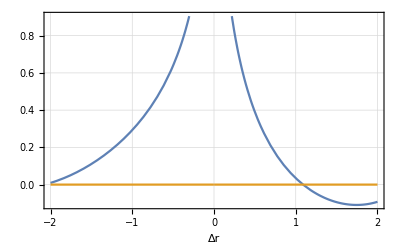
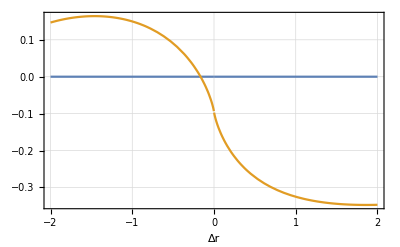
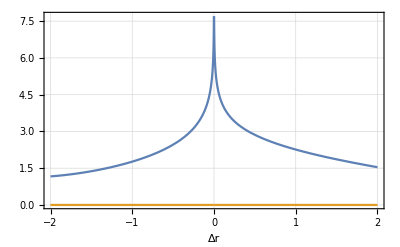
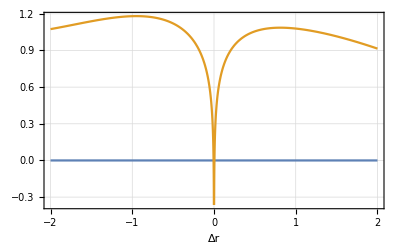
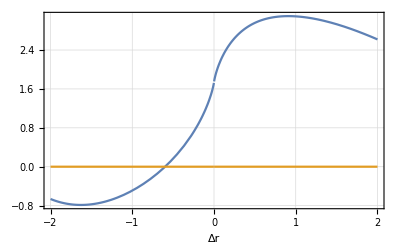
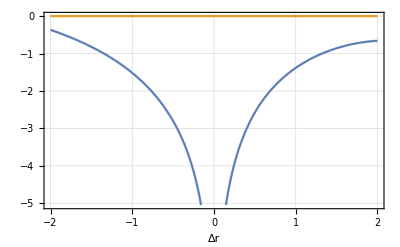
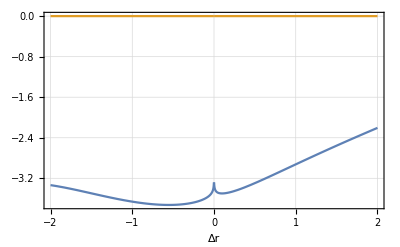

```mathematica
Table[plothSS[i,2,2][7.6],{i,1,7}]
```

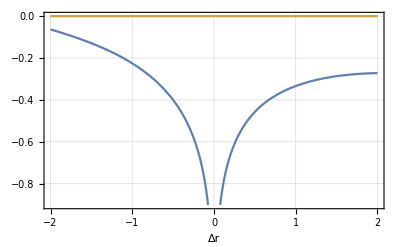
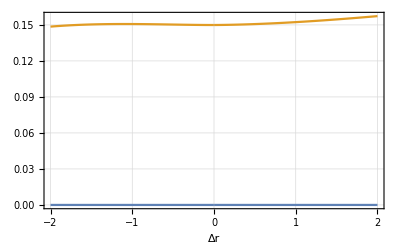
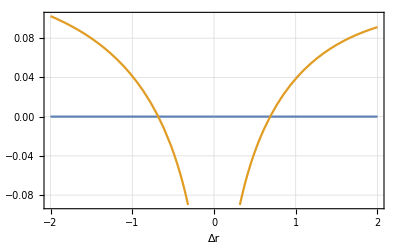

```mathematica
Table[plothSS[i,2,1][7.6],{i,8,10}]
```

## The other punctures

Evaluating the other punctures requires the user to supply first-order data such as h_ab^R1 and its covariant derivatives, F_r^1,(ṙ)_0, etc

```mathematica
Block[{M=1,r0=7.6,Δr=0.4,Ω=7.6^(-3/2)},h2P["ms",1,2,2]]
```

(0.-1.30478 ⅈ) r0dot

```mathematica
Block[{M=1,r0=7.6,Δr=0.4,Ω=7.6^(-3/2)},h2P["δz",1,2,2]]
```

-109.278 Fr

```mathematica
Block[{M=1,r0=7.6,Δr=0.4,Ω=7.6^(-3/2)},h2P["SR",1,2,2]]
```

2 π (1/2 ⅈ (0.337386 DhR1[1,1,1]+0.106883 DhR1[1,1,4]+0.29464 DhR1[1,2,2]+0.00426383 DhR1[1,3,3]-0.0754774 DhR1[1,4,1]-0.000627938 DhR1[1,4,4]-0.17256 DhR1[2,2,1]-0.0961079 DhR1[2,2,4]+0.116758 DhR1[2,4,2]+0.000757813 DhR1[3,3,1]-0.00105846 DhR1[3,3,4]+0.00223964 DhR1[3,4,3]+0.00735994 DhR1[4,4,1]+0.00104376 DhR1[4,4,4]+0.0256 (-0.00173893 DhR1[1,1,1]+0.0000202005 DhR1[1,1,4]-0.000497914 DhR1[1,2,2]-0.0000133478 DhR1[1,3,3]-6.99909×10^-6 DhR1[1,4,1]+0.0000241798 DhR1[1,4,4]-0.00032089 DhR1[2,2,1]+0.000267656 DhR1[2,2,4]+0.0000595985 DhR1[2,4,2]-3.84503×10^-6 DhR1[3,3,1]+2.22932×10^-6 DhR1[3,3,4]-7.01112×10^-6 DhR1[3,4,3]-0.0000103918 DhR1[4,4,1]-2.11538×10^-6 DhR1[4,4,4]-0.00026206 hR1[1,2]-0.0000888886 hR1[2,4])+0.16 (-0.0363175 DhR1[1,1,1]-0.00253279 DhR1[1,1,4]-0.0156798 DhR1[1,2,2]-0.000318928 DhR1[1,3,3]+0.0019195 DhR1[1,4,1]+0.000393758 DhR1[1,4,4]-0.000440053 DhR1[2,2,1]+0.00676804 DhR1[2,2,4]-0.00216833 DhR1[2,4,2]-0.0000858092 DhR1[3,3,1]+0.0000641423 DhR1[3,3,4]-0.000167522 DhR1[3,4,3]-0.000354339 DhR1[4,4,1]-0.0000619604 DhR1[4,4,4]-0.00412625 hR1[1,2]+0.4 (0.0108142 DhR1[1,1,1]+0.000225674 DhR1[1,1,4]+0.00372433 DhR1[1,2,2]+0.0000875078 DhR1[1,3,3]-0.000203102 DhR1[1,4,1]-0.000136969 DhR1[1,4,4]+0.00125108 DhR1[2,2,1]-0.00180458 DhR1[2,2,4]+0.0000346214 DhR1[2,4,2]+0.0000248848 DhR1[3,3,1]-0.0000160091 DhR1[3,3,4]+0.0000459648 DhR1[3,4,3]+0.0000806318 DhR1[4,4,1]+0.000015324 DhR1[4,4,4]+0.00147013 hR1[1,2]+0.000228455 hR1[2,4])+0.000181873 hR1[2,4])+0.064 (0.00271008 DDhR1[1,1,1,2]-0.00272354 DDhR1[1,1,2,4]-0.0199974 DDhR1[1,2,1,1]+0.00181635 DDhR1[1,2,1,4]-0.00783988 DDhR1[1,2,2,2]+0.000278297 DDhR1[1,2,4,4]-0.000151216 DDhR1[1,3,2,3]+0.00240202 DDhR1[1,4,1,2]+0.000239581 DDhR1[1,4,2,4]+0.00174537 DDhR1[2,2,1,2]+0.00416182 DDhR1[2,2,2,4]+0.000232261 DDhR1[2,3,1,3]-0.0000348922 DDhR1[2,3,4,3]+0.00206005 DDhR1[2,4,1,1]+0.000331103 DDhR1[2,4,1,4]-0.00175835 DDhR1[2,4,2,2]-0.0000195057 DDhR1[2,4,3,3]-0.0000379282 DDhR1[2,4,4,4]-0.000174685 DDhR1[3,3,1,2]+0.0000453093 DDhR1[3,3,2,4]-0.0000794284 DDhR1[3,4,2,3]-0.000264659 DDhR1[4,4,1,2]-5.59819×10^-6 DDhR1[4,4,2,4]+0.00529337 DhR1[1,1,1]-0.000739082 DhR1[1,1,4]+0.00668097 DhR1[1,2,2]+0.000136306 DhR1[1,3,3]+0.000155722 DhR1[1,4,1]-0.0000195117 DhR1[1,4,4]-0.00721956 DhR1[2,2,1]-0.00100043 DhR1[2,2,4]+0.00211034 DhR1[2,4,2]+0.0000358547 DhR1[3,3,1]-0.000019956 DhR1[3,3,4]+0.0000284253 DhR1[3,4,3]+0.0000688446 DhR1[4,4,1]+6.80964×10^-6 DhR1[4,4,4]+0.00104261 hR1[1,2]+0.4 (0.0000855764 DDhR1[1,1,1,2]+0.000361482 DDhR1[1,1,2,4]+0.00474987 DDhR1[1,2,1,1]-0.000431427 DDhR1[1,2,1,4]+0.00186217 DDhR1[1,2,2,2]-0.0000661025 DDhR1[1,2,4,4]+0.0000437539 DDhR1[1,3,2,3]-0.000486263 DDhR1[1,4,1,2]-0.0000898896 DDhR1[1,4,2,4]-0.000032383 DDhR1[2,2,1,2]-0.00113811 DDhR1[2,2,2,4]-0.0000605939 DDhR1[2,3,1,3]+0.0000104114 DDhR1[2,3,4,3]-0.000442419 DDhR1[2,4,1,1]-0.0000844642 DDhR1[2,4,1,4]+0.000257516 DDhR1[2,4,2,2]+5.64392×10^-6 DDhR1[2,4,3,3]+0.0000108847 DDhR1[2,4,4,4]+0.000042993 DDhR1[3,3,1,2]-0.0000113495 DDhR1[3,3,2,4]+0.0000229824 DDhR1[3,4,2,3]+0.0000616856 DDhR1[4,4,1,2]+1.79053×10^-6 DDhR1[4,4,2,4]-0.00279636 DhR1[1,1,1]+0.000260518 DhR1[1,1,4]-0.00166265 DhR1[1,2,2]-0.0000448231 DhR1[1,3,3]-0.0000743283 DhR1[1,4,1]+0.0000258533 DhR1[1,4,4]+0.00166052 DhR1[2,2,1]+0.000383869 DhR1[2,2,4]-0.000514378 DhR1[2,4,2]-0.000016496 DhR1[3,3,1]+7.12171×10^-6 DhR1[3,3,4]-0.0000114681 DhR1[3,4,3]-0.0000264682 DhR1[4,4,1]-2.39243×10^-6 DhR1[4,4,4]-0.000501706 hR1[1,2]-0.0000606685 hR1[2,4])+0.00041453 hR1[2,4])+0.4 (-0.165945 DDhR1[1,1,1,2]+0.096194 DDhR1[1,1,2,4]+0.375772 DDhR1[1,2,1,1]-0.0341311 DDhR1[1,2,1,4]+0.14732 DDhR1[1,2,2,2]-0.0052295 DDhR1[1,2,4,4]+0.00168873 DDhR1[1,3,2,3]-0.0582724 DDhR1[1,4,1,2]+0.000639115 DDhR1[1,4,2,4]-0.0930738 DDhR1[2,2,1,2]-0.0546144 DDhR1[2,2,2,4]-0.0035662 DDhR1[2,3,1,3]+0.000343254 DDhR1[2,3,4,3]-0.0463216 DDhR1[2,4,1,1]-0.00527728 DDhR1[2,4,1,4]+0.0583789 DDhR1[2,4,2,2]+0.000217833 DDhR1[2,4,3,3]+0.000408249 DDhR1[2,4,4,4]+0.00299764 DDhR1[3,3,1,2]-0.000739916 DDhR1[3,3,2,4]+0.000887032 DDhR1[3,4,2,3]+0.00520707 DDhR1[4,4,1,2]+0.0000136748 DDhR1[4,4,2,4]+0.0546028 DhR1[1,1,1]+0.0158858 DhR1[1,1,4]-0.113426 DhR1[1,2,2]-0.00108781 DhR1[1,3,3]-0.00746627 DhR1[1,4,1]-0.00120145 DhR1[1,4,4]+0.0975888 DhR1[2,2,1]+0.00362243 DhR1[2,2,4]-0.0179204 DhR1[2,4,2]+0.000378863 DhR1[3,3,1]+0.000033821 DhR1[3,3,4]-0.0000281206 DhR1[3,4,3]+0.000472224 DhR1[4,4,1]-0.0000327193 DhR1[4,4,4]+0.000580997 hR1[1,2]+0.00758264 hR1[2,4])-0.00715204 hR1[2,4])-1/2 ⅈ (-0.337386 DhR1[1,1,1]-0.106883 DhR1[1,1,4]-0.29464 DhR1[1,2,2]-0.00426383 DhR1[1,3,3]+0.0754774 DhR1[1,4,1]+0.000627938 DhR1[1,4,4]+0.17256 DhR1[2,2,1]+0.0961079 DhR1[2,2,4]-0.116758 DhR1[2,4,2]-0.000757813 DhR1[3,3,1]+0.00105846 DhR1[3,3,4]-0.00223964 DhR1[3,4,3]-0.00735994 DhR1[4,4,1]-0.00104376 DhR1[4,4,4]-0.0256 (-0.00173893 DhR1[1,1,1]+0.0000202005 DhR1[1,1,4]-0.000497914 DhR1[1,2,2]-0.0000133478 DhR1[1,3,3]-6.99909×10^-6 DhR1[1,4,1]+0.0000241798 DhR1[1,4,4]-0.00032089 DhR1[2,2,1]+0.000267656 DhR1[2,2,4]+0.0000595985 DhR1[2,4,2]-3.84503×10^-6 DhR1[3,3,1]+2.22932×10^-6 DhR1[3,3,4]-7.01112×10^-6 DhR1[3,4,3]-0.0000103918 DhR1[4,4,1]-2.11538×10^-6 DhR1[4,4,4]-0.00026206 hR1[1,2]-0.0000888886 hR1[2,4])-0.16 (-0.0363175 DhR1[1,1,1]-0.00253279 DhR1[1,1,4]-0.0156798 DhR1[1,2,2]-0.000318928 DhR1[1,3,3]+0.0019195 DhR1[1,4,1]+0.000393758 DhR1[1,4,4]-0.000440053 DhR1[2,2,1]+0.00676804 DhR1[2,2,4]-0.00216833 DhR1[2,4,2]-0.0000858092 DhR1[3,3,1]+0.0000641423 DhR1[3,3,4]-0.000167522 DhR1[3,4,3]-0.000354339 DhR1[4,4,1]-0.0000619604 DhR1[4,4,4]-0.00412625 hR1[1,2]+0.4 (0.0108142 DhR1[1,1,1]+0.000225674 DhR1[1,1,4]+0.00372433 DhR1[1,2,2]+0.0000875078 DhR1[1,3,3]-0.000203102 DhR1[1,4,1]-0.000136969 DhR1[1,4,4]+0.00125108 DhR1[2,2,1]-0.00180458 DhR1[2,2,4]+0.0000346214 DhR1[2,4,2]+0.0000248848 DhR1[3,3,1]-0.0000160091 DhR1[3,3,4]+0.0000459648 DhR1[3,4,3]+0.0000806318 DhR1[4,4,1]+0.000015324 DhR1[4,4,4]+0.00147013 hR1[1,2]+0.000228455 hR1[2,4])+0.000181873 hR1[2,4])-0.064 (0.00271008 DDhR1[1,1,1,2]-0.00272354 DDhR1[1,1,2,4]-0.0199974 DDhR1[1,2,1,1]+0.00181635 DDhR1[1,2,1,4]-0.00783988 DDhR1[1,2,2,2]+0.000278297 DDhR1[1,2,4,4]-0.000151216 DDhR1[1,3,2,3]+0.00240202 DDhR1[1,4,1,2]+0.000239581 DDhR1[1,4,2,4]+0.00174537 DDhR1[2,2,1,2]+0.00416182 DDhR1[2,2,2,4]+0.000232261 DDhR1[2,3,1,3]-0.0000348922 DDhR1[2,3,4,3]+0.00206005 DDhR1[2,4,1,1]+0.000331103 DDhR1[2,4,1,4]-0.00175835 DDhR1[2,4,2,2]-0.0000195057 DDhR1[2,4,3,3]-0.0000379282 DDhR1[2,4,4,4]-0.000174685 DDhR1[3,3,1,2]+0.0000453093 DDhR1[3,3,2,4]-0.0000794284 DDhR1[3,4,2,3]-0.000264659 DDhR1[4,4,1,2]-5.59819×10^-6 DDhR1[4,4,2,4]+0.00529337 DhR1[1,1,1]-0.000739082 DhR1[1,1,4]+0.00668097 DhR1[1,2,2]+0.000136306 DhR1[1,3,3]+0.000155722 DhR1[1,4,1]-0.0000195117 DhR1[1,4,4]-0.00721956 DhR1[2,2,1]-0.00100043 DhR1[2,2,4]+0.00211034 DhR1[2,4,2]+0.0000358547 DhR1[3,3,1]-0.000019956 DhR1[3,3,4]+0.0000284253 DhR1[3,4,3]+0.0000688446 DhR1[4,4,1]+6.80964×10^-6 DhR1[4,4,4]+0.00104261 hR1[1,2]+0.4 (0.0000855764 DDhR1[1,1,1,2]+0.000361482 DDhR1[1,1,2,4]+0.00474987 DDhR1[1,2,1,1]-0.000431427 DDhR1[1,2,1,4]+0.00186217 DDhR1[1,2,2,2]-0.0000661025 DDhR1[1,2,4,4]+0.0000437539 DDhR1[1,3,2,3]-0.000486263 DDhR1[1,4,1,2]-0.0000898896 DDhR1[1,4,2,4]-0.000032383 DDhR1[2,2,1,2]-0.00113811 DDhR1[2,2,2,4]-0.0000605939 DDhR1[2,3,1,3]+0.0000104114 DDhR1[2,3,4,3]-0.000442419 DDhR1[2,4,1,1]-0.0000844642 DDhR1[2,4,1,4]+0.000257516 DDhR1[2,4,2,2]+5.64392×10^-6 DDhR1[2,4,3,3]+0.0000108847 DDhR1[2,4,4,4]+0.000042993 DDhR1[3,3,1,2]-0.0000113495 DDhR1[3,3,2,4]+0.0000229824 DDhR1[3,4,2,3]+0.0000616856 DDhR1[4,4,1,2]+1.79053×10^-6 DDhR1[4,4,2,4]-0.00279636 DhR1[1,1,1]+0.000260518 DhR1[1,1,4]-0.00166265 DhR1[1,2,2]-0.0000448231 DhR1[1,3,3]-0.0000743283 DhR1[1,4,1]+0.0000258533 DhR1[1,4,4]+0.00166052 DhR1[2,2,1]+0.000383869 DhR1[2,2,4]-0.000514378 DhR1[2,4,2]-0.000016496 DhR1[3,3,1]+7.12171×10^-6 DhR1[3,3,4]-0.0000114681 DhR1[3,4,3]-0.0000264682 DhR1[4,4,1]-2.39243×10^-6 DhR1[4,4,4]-0.000501706 hR1[1,2]-0.0000606685 hR1[2,4])+0.00041453 hR1[2,4])-0.4 (-0.165945 DDhR1[1,1,1,2]+0.096194 DDhR1[1,1,2,4]+0.375772 DDhR1[1,2,1,1]-0.0341311 DDhR1[1,2,1,4]+0.14732 DDhR1[1,2,2,2]-0.0052295 DDhR1[1,2,4,4]+0.00168873 DDhR1[1,3,2,3]-0.0582724 DDhR1[1,4,1,2]+0.000639115 DDhR1[1,4,2,4]-0.0930738 DDhR1[2,2,1,2]-0.0546144 DDhR1[2,2,2,4]-0.0035662 DDhR1[2,3,1,3]+0.000343254 DDhR1[2,3,4,3]-0.0463216 DDhR1[2,4,1,1]-0.00527728 DDhR1[2,4,1,4]+0.0583789 DDhR1[2,4,2,2]+0.000217833 DDhR1[2,4,3,3]+0.000408249 DDhR1[2,4,4,4]+0.00299764 DDhR1[3,3,1,2]-0.000739916 DDhR1[3,3,2,4]+0.000887032 DDhR1[3,4,2,3]+0.00520707 DDhR1[4,4,1,2]+0.0000136748 DDhR1[4,4,2,4]+0.0546028 DhR1[1,1,1]+0.0158858 DhR1[1,1,4]-0.113426 DhR1[1,2,2]-0.00108781 DhR1[1,3,3]-0.00746627 DhR1[1,4,1]-0.00120145 DhR1[1,4,4]+0.0975888 DhR1[2,2,1]+0.00362243 DhR1[2,2,4]-0.0179204 DhR1[2,4,2]+0.000378863 DhR1[3,3,1]+0.000033821 DhR1[3,3,4]-0.0000281206 DhR1[3,4,3]+0.000472224 DhR1[4,4,1]-0.0000327193 DhR1[4,4,4]+0.000580997 hR1[1,2]+0.00758264 hR1[2,4])+0.00715204 hR1[2,4])+1/2 (-1.86602 DDhR1[1,1,1,1]-0.321133 DDhR1[1,1,1,4]-1.75993 DDhR1[1,1,2,2]-0.164056 DDhR1[1,1,3,3]+0.0597951 DDhR1[1,1,4,4]+1.99713 DDhR1[1,2,1,2]+0.375007 DDhR1[1,2,2,4]+0.184298 DDhR1[1,3,1,3]+0.0136524 DDhR1[1,3,4,3]+0.0494775 DDhR1[1,4,1,1]-0.0364675 DDhR1[1,4,1,4]-0.0949681 DDhR1[1,4,2,2]-0.00651072 DDhR1[1,4,3,3]+0.000712516 DDhR1[1,4,4,4]-0.645044 DDhR1[2,2,1,1]+0.200502 DDhR1[2,2,1,4]+0.106357 DDhR1[2,2,2,2]+0.0876615 DDhR1[2,2,3,3]-0.0655678 DDhR1[2,2,4,4]-0.098165 DDhR1[2,3,2,3]-0.482808 DDhR1[2,4,1,2]+0.0779314 DDhR1[2,4,2,4]+0.0683843 DDhR1[3,3,1,1]+0.0127597 DDhR1[3,3,1,4]-0.0158454 DDhR1[3,3,2,2]-0.0012963 DDhR1[3,3,3,3]-0.000634578 DDhR1[3,3,4,4]-0.0160692 DDhR1[3,4,1,3]-0.000914621 DDhR1[3,4,4,3]-0.136998 DDhR1[4,4,1,1]-0.00756943 DDhR1[4,4,1,4]+0.00730764 DDhR1[4,4,2,2]+0.00131334 DDhR1[4,4,3,3]+0.000629722 DDhR1[4,4,4,4]-0.304956 DhR1[1,1,2]+0.0611112 DhR1[1,2,1]-0.0402065 DhR1[1,2,4]-0.085218 DhR1[1,4,2]-0.0643221 DhR1[2,2,2]+0.0235589 DhR1[2,3,3]+0.0477068 DhR1[2,4,1]-0.01997 DhR1[2,4,4]-0.00477438 DhR1[3,3,2]+0.000411579 DhR1[4,4,2]-0.0153496 hR1[1,1]-0.00765399 hR1[1,4]-0.000786525 hR1[2,2]+0.000576699 hR1[3,3]-0.064 (0.000166447 DhR1[1,1,2]+0.00106367 DhR1[1,2,1]+0.000086151 DhR1[1,2,4]+0.000263491 DhR1[1,4,2]+0.000564397 DhR1[2,2,2]-0.0000859561 DhR1[2,3,3]-0.000208255 DhR1[2,4,1]+0.0000263258 DhR1[2,4,4]-0.0000500097 DhR1[3,3,2]+0.0000622391 DhR1[4,4,2]-0.000847528 hR1[1,1]-0.000292502 hR1[1,4]+0.0000837772 hR1[2,2]+0.0000222647 hR1[3,3]+0.4 (-0.000090019 DhR1[1,1,2]-0.000226705 DhR1[1,2,1]-0.0000183618 DhR1[1,2,4]-0.0000634389 DhR1[1,4,2]-0.000148876 DhR1[2,2,2]+0.0000190877 DhR1[2,3,3]+0.0000422321 DhR1[2,4,1]-5.24078×10^-6 DhR1[2,4,4]+0.0000108489 DhR1[3,3,2]-0.0000134796 DhR1[4,4,2]+0.000257058 hR1[1,1]+0.0000780604 hR1[1,4]+2.92712×10^-6 hR1[2,2]-6.54017×10^-6 hR1[3,3]+9.75067×10^-6 hR1[4,4])-0.000035045 hR1[4,4])-0.0256 (0.000822988 DDhR1[1,1,1,1]+0.0000346156 DDhR1[1,1,1,4]+0.000236242 DDhR1[1,1,2,2]+7.76384×10^-6 DDhR1[1,1,3,3]+2.61182×10^-6 DDhR1[1,1,4,4]+0.00013985 DDhR1[1,2,1,2]-0.0000155182 DDhR1[1,2,2,4]-0.0000392228 DDhR1[1,3,1,3]-2.64442×10^-6 DDhR1[1,3,4,3]+0.0000621542 DDhR1[1,4,1,1]+3.83798×10^-6 DDhR1[1,4,1,4]+0.0000994241 DDhR1[1,4,2,2]-2.73672×10^-6 DDhR1[1,4,3,3]+7.74188×10^-7 DDhR1[1,4,4,4]+0.000422412 DDhR1[2,2,1,1]-0.000033489 DDhR1[2,2,1,4]+0.000181991 DDhR1[2,2,2,2]-0.0000321061 DDhR1[2,2,3,3]+0.00001466 DDhR1[2,2,4,4]-0.0000342468 DDhR1[2,3,2,3]-3.08323×10^-6 DDhR1[2,4,1,2]+0.0000111354 DDhR1[2,4,2,4]-0.0000101543 DDhR1[3,3,1,1]-2.37768×10^-6 DDhR1[3,3,1,4]-0.0000129531 DDhR1[3,3,2,2]+5.5351×10^-7 DDhR1[3,3,3,3]+1.99528×10^-7 DDhR1[3,3,4,4]+2.47464×10^-6 DDhR1[3,4,1,3]+2.94817×10^-7 DDhR1[3,4,4,3]+0.0000212784 DDhR1[4,4,1,1]+1.66059×10^-6 DDhR1[4,4,1,4]+0.0000204961 DDhR1[4,4,2,2]-5.68592×10^-7 DDhR1[4,4,3,3]-1.94377×10^-7 DDhR1[4,4,4,4]-0.000285829 DhR1[1,1,2]+0.0000536451 DhR1[1,2,1]-0.0000152468 DhR1[1,2,4]-0.000115937 DhR1[1,4,2]+0.0000551862 DhR1[2,2,2]-6.19809×10^-6 DhR1[2,3,3]+7.05232×10^-6 DhR1[2,4,1]-5.63716×10^-7 DhR1[2,4,4]+8.9914×10^-6 DhR1[3,3,2]-0.0000150648 DhR1[4,4,2]+0.000339166 hR1[1,1]+0.000109917 hR1[1,4]+0.000050219 hR1[2,2]-9.59429×10^-6 hR1[3,3]+0.0000127411 hR1[4,4])-0.16 (-0.024594 DDhR1[1,1,1,1]-0.00181084 DDhR1[1,1,1,4]-0.00781444 DDhR1[1,1,2,2]-0.000804288 DDhR1[1,1,3,3]+0.000136653 DDhR1[1,1,4,4]+0.0044071 DDhR1[1,2,1,2]+0.00169072 DDhR1[1,2,2,4]+0.00148694 DDhR1[1,3,1,3]+0.000105467 DDhR1[1,3,4,3]-0.00118281 DDhR1[1,4,1,1]-0.000203443 DDhR1[1,4,1,4]-0.00195171 DDhR1[1,4,2,2]+0.0000263408 DDhR1[1,4,3,3]-0.0000162798 DDhR1[1,4,4,4]-0.0115121 DDhR1[2,2,1,1]+0.00146876 DDhR1[2,2,1,4]-0.00154767 DDhR1[2,2,2,2]+0.000964414 DDhR1[2,2,3,3]-0.0005578 DDhR1[2,2,4,4]+0.000260256 DDhR1[2,3,2,3]-0.00154536 DDhR1[2,4,1,2]-5.56876×10^-6 DDhR1[2,4,2,4]+0.000456823 DDhR1[3,3,1,1]+0.000096413 DDhR1[3,3,1,4]+0.000201282 DDhR1[3,3,2,2]-0.0000157957 DDhR1[3,3,3,3]-6.603×10^-6 DDhR1[3,3,4,4]-0.000110962 DDhR1[3,4,1,3]-9.12524×10^-6 DDhR1[3,4,4,3]-0.000939238 DDhR1[4,4,1,1]-0.0000625573 DDhR1[4,4,1,4]-0.000388157 DDhR1[4,4,2,2]+0.0000161521 DDhR1[4,4,3,3]+6.46645×10^-6 DDhR1[4,4,4,4]+0.00350745 DhR1[1,1,2]-0.00481031 DhR1[1,2,1]-0.000089109 DhR1[1,2,4]+0.00113863 DhR1[1,4,2]-0.00186982 DhR1[2,2,2]+0.000472456 DhR1[2,3,3]+0.00084536 DhR1[2,4,1]-0.000168816 DhR1[2,4,4]-0.0000597838 DhR1[3,3,2]+0.0000837254 DhR1[4,4,2]-0.000133397 hR1[1,1]-0.000304529 hR1[1,4]+0.000575834 hR1[2,2]-0.000029484 hR1[3,3]+0.4 (-0.000543295 hR1[1,1]-0.000144578 hR1[1,4]-0.000284715 hR1[2,2]+0.0000242001 hR1[3,3]-0.0000244412 hR1[4,4])+0.0000142524 hR1[4,4])-0.4 (0.00716737 DhR1[1,1,2]-0.0221726 DhR1[1,2,1]-0.00179585 DhR1[1,2,4]-0.00408571 DhR1[1,4,2]-0.0061907 DhR1[2,2,2]+0.00164688 DhR1[2,3,3]+0.00477907 DhR1[2,4,1]-0.000624015 DhR1[2,4,4]+0.00100937 DhR1[3,3,2]-0.00125958 DhR1[4,4,2]+0.0080352 hR1[1,1]+0.003733 hR1[1,4]-0.00304636 hR1[2,2]-0.000129187 hR1[3,3]+0.00030327 hR1[4,4])-0.000754032 hR1[4,4])+1/2 √(3/2) (-0.278784 DDhR1[1,1,1,1]-0.367374 DDhR1[1,1,1,4]-7.9771 DDhR1[1,1,2,2]-0.0928944 DDhR1[1,1,3,3]-0.115642 DDhR1[1,1,4,4]+13.7338 DDhR1[1,2,1,2]+0.719538 DDhR1[1,2,2,4]+0.136544 DDhR1[1,3,1,3]+0.00214022 DDhR1[1,3,4,3]+0.274966 DDhR1[1,4,1,1]+0.181541 DDhR1[1,4,1,4]-0.637535 DDhR1[1,4,2,2]-0.00278337 DDhR1[1,4,3,3]-0.000230441 DDhR1[1,4,4,4]-4.84984 DDhR1[2,2,1,1]-0.227283 DDhR1[2,2,1,4]+0.230234 DDhR1[2,2,2,2]-0.0131655 DDhR1[2,2,3,3]-0.0174224 DDhR1[2,2,4,4]+0.0225708 DDhR1[2,3,2,3]+0.201077 DDhR1[2,4,1,2]+0.0415202 DDhR1[2,4,2,4]-0.0547567 DDhR1[3,3,1,1]+0.00201338 DDhR1[3,3,1,4]-0.0129463 DDhR1[3,3,2,2]-0.00011557 DDhR1[3,3,3,3]+0.000191722 DDhR1[3,3,4,4]-0.00574137 DDhR1[3,4,1,3]-0.000620229 DDhR1[3,4,4,3]-0.0961922 DDhR1[4,4,1,1]-0.00442664 DDhR1[4,4,1,4]-0.0238531 DDhR1[4,4,2,2]+0.000116166 DDhR1[4,4,3,3]-0.000190309 DDhR1[4,4,4,4]-0.351252 DhR1[1,1,2]+0.355633 DhR1[1,2,1]+0.00718366 DhR1[1,2,4]-0.0259354 DhR1[1,4,2]-0.140497 DhR1[2,2,2]-0.01126 DhR1[2,3,3]-0.0147693 DhR1[2,4,1]-0.0110977 DhR1[2,4,4]+0.00389483 DhR1[3,3,2]+0.00342138 DhR1[4,4,2]+0.0646626 hR1[1,1]+0.00645074 hR1[1,4]+0.0724259 hR1[2,2]-0.000772307 hR1[3,3]+0.4 (-0.168976 hR1[1,1]-0.0222118 hR1[1,4]-0.0885524 hR1[2,2]+0.000483366 hR1[3,3]-0.000558339 hR1[4,4])+0.4 (-0.523433 DhR1[1,1,2]+0.725124 DhR1[1,2,1]+0.0587308 DhR1[1,2,4]-0.0208883 DhR1[1,4,2]+0.0509899 DhR1[2,2,2]-0.00688095 DhR1[2,3,3]-0.00716093 DhR1[2,4,1]-0.00521682 DhR1[2,4,4]+0.00388096 DhR1[3,3,2]+0.0041735 DhR1[4,4,2]-0.0555003 hR1[1,1]-0.00571208 hR1[1,4]+0.0203406 hR1[2,2]-0.000640456 hR1[3,3]+0.4 (0.127582 DhR1[1,1,2]-0.264702 DhR1[1,2,1]-0.0214393 DhR1[1,2,4]-0.000772525 DhR1[1,4,2]-0.0518875 DhR1[2,2,2]+0.00337679 DhR1[2,3,3]+0.00235352 DhR1[2,4,4]-0.00121916 DhR1[3,3,2]-0.00174923 DhR1[4,4,2]+0.0647615 hR1[1,1]+0.0074109 hR1[1,4]-0.00647388 hR1[2,2]+0.000463013 hR1[3,3]+0.000515258 hR1[4,4])-0.000545487 hR1[4,4])+0.064 (-0.011665 DhR1[1,1,2]+0.0483721 DhR1[1,2,1]+0.00391786 DhR1[1,2,4]+0.00170067 DhR1[1,4,2]+0.015587 DhR1[2,2,2]-0.000782713 DhR1[2,3,3]+0.000453669 DhR1[2,4,1]-0.000508038 DhR1[2,4,4]+0.000180747 DhR1[3,3,2]+0.000366873 DhR1[4,4,2]-0.0238559 hR1[1,1]-0.00285797 hR1[1,4]-0.000998555 hR1[2,2]-0.000113175 hR1[3,3]+0.4 (-3.60753×10^-6 DhR1[1,1,2]-0.00566418 DhR1[1,2,1]-0.000458766 DhR1[1,2,4]-0.000384653 DhR1[1,4,2]-0.00254289 DhR1[2,2,2]+0.000111929 DhR1[2,3,3]-0.000103447 DhR1[2,4,1]+0.0000681361 DhR1[2,4,4]-0.0000155491 DhR1[3,3,2]-0.0000491825 DhR1[4,4,2]+0.00465681 hR1[1,1]+0.000573975 hR1[1,4]+0.000607689 hR1[2,2]+0.0000146982 hR1[3,3]+0.0000304302 hR1[4,4])-0.000167692 hR1[4,4])+0.0256 (0.00868698 DDhR1[1,1,1,1]+0.00148036 DDhR1[1,1,1,4]+0.00513345 DDhR1[1,1,2,2]+0.000211713 DDhR1[1,1,3,3]+0.000235684 DDhR1[1,1,4,4]-0.00325734 DDhR1[1,2,1,2]+0.000946754 DDhR1[1,2,2,4]-0.000567849 DDhR1[1,3,1,3]-0.0000153569 DDhR1[1,3,4,3]+0.00133742 DDhR1[1,4,1,1]-0.000283675 DDhR1[1,4,1,4]+0.00152255 DDhR1[1,4,2,2]-0.0000101459 DDhR1[1,4,3,3]-0.0000135765 DDhR1[1,4,4,4]+0.0155524 DDhR1[2,2,1,1]+0.00143376 DDhR1[2,2,1,4]+0.00533638 DDhR1[2,2,2,2]-0.000215412 DDhR1[2,2,3,3]-0.000125205 DDhR1[2,2,4,4]-0.000298124 DDhR1[2,3,2,3]-0.00105665 DDhR1[2,4,1,2]-0.000244019 DDhR1[2,4,2,4]+0.0000664191 DDhR1[3,3,1,1]+4.6608×10^-6 DDhR1[3,3,1,4]+0.000126982 DDhR1[3,3,2,2]+2.80568×10^-6 DDhR1[3,3,3,3]-1.10544×10^-6 DDhR1[3,3,4,4]-4.93989×10^-6 DDhR1[3,4,1,3]+7.26649×10^-6 DDhR1[3,4,4,3]+0.000166635 DDhR1[4,4,1,1]+9.40255×10^-6 DDhR1[4,4,1,4]+0.000213557 DDhR1[4,4,2,2]-2.91559×10^-6 DDhR1[4,4,3,3]+1.04319×10^-6 DDhR1[4,4,4,4]-0.00512562 DhR1[1,1,2]-0.00855431 DhR1[1,2,1]-0.000624049 DhR1[1,2,4]-0.00113349 DhR1[1,4,2]-0.00151967 DhR1[2,2,2]-7.06221×10^-7 DhR1[2,3,3]+0.0000171227 DhR1[2,4,1]+9.1941×10^-6 DhR1[2,4,4]-0.000108856 DhR1[3,3,2]-0.000130355 DhR1[4,4,2]+0.00854707 hR1[1,1]+0.00102484 hR1[1,4]+0.000518808 hR1[2,2]+0.0000353925 hR1[3,3]+0.0000614522 hR1[4,4])+0.16 (0.157081 DDhR1[1,1,1,1]+0.0295345 DDhR1[1,1,1,4]+0.183303 DDhR1[1,1,2,2]+0.00708637 DDhR1[1,1,3,3]+0.00770493 DDhR1[1,1,4,4]-0.433162 DDhR1[1,2,1,2]-0.00563012 DDhR1[1,2,2,4]-0.0120316 DDhR1[1,3,1,3]-0.000318201 DDhR1[1,3,4,3]+0.0148025 DDhR1[1,4,1,1]-0.00970808 DDhR1[1,4,1,4]+0.0252015 DDhR1[1,4,2,2]+0.000138955 DDhR1[1,4,3,3]-0.0000987 DDhR1[1,4,4,4]+0.380023 DDhR1[2,2,1,1]+0.026747 DDhR1[2,2,1,4]+0.0127475 DDhR1[2,2,2,2]-0.00197736 DDhR1[2,2,3,3]-0.00101854 DDhR1[2,2,4,4]-0.00198334 DDhR1[2,3,2,3]-0.0267141 DDhR1[2,4,1,2]-0.00291516 DDhR1[2,4,2,4]+0.00266288 DDhR1[3,3,1,1]+0.0000222125 DDhR1[3,3,1,4]+0.00264013 DDhR1[3,3,2,2]+0.0000319112 DDhR1[3,3,3,3]-0.0000208474 DDhR1[3,3,4,4]+0.000127426 DDhR1[3,4,1,3]+0.000102449 DDhR1[3,4,4,3]+0.00501025 DDhR1[4,4,1,1]+0.000261394 DDhR1[4,4,1,4]+0.0034393 DDhR1[4,4,2,2]-0.0000328958 DDhR1[4,4,3,3]+0.0000202445 DDhR1[4,4,4,4]-0.0297974 DhR1[1,1,2]-0.0105048 DhR1[1,2,1]-0.0010634 DhR1[1,2,4]-0.00479297 DhR1[1,4,2]-0.00667362 DhR1[2,2,2]-0.000823136 DhR1[2,3,3]+0.000488007 DhR1[2,4,1]-0.000603521 DhR1[2,4,4]-0.000486253 DhR1[3,3,2]-0.000471224 DhR1[4,4,2]+0.0728155 hR1[1,1]+0.00923945 hR1[1,4]+0.0277427 hR1[2,2]-0.0000581657 hR1[3,3]+0.4 (-0.051871 DDhR1[1,1,1,1]-0.00882973 DDhR1[1,1,1,4]-0.0339275 DDhR1[1,1,2,2]-0.0017217 DDhR1[1,1,3,3]-0.00185118 DDhR1[1,1,4,4]+0.0646757 DDhR1[1,2,1,2]-0.00278339 DDhR1[1,2,2,4]+0.0035181 DDhR1[1,3,1,3]+0.0000964644 DDhR1[1,3,4,3]-0.00681842 DDhR1[1,4,1,1]+0.002239 DDhR1[1,4,1,4]-0.00766145 DDhR1[1,4,2,2]+6.05048×10^-6 DDhR1[1,4,3,3]+0.0000559172 DDhR1[1,4,4,4]-0.103638 DDhR1[2,2,1,1]-0.00842544 DDhR1[2,2,1,4]-0.0172958 DDhR1[2,2,2,2]+0.000969186 DDhR1[2,2,3,3]+0.000560026 DDhR1[2,2,4,4]+0.0011256 DDhR1[2,3,2,3]+0.00740394 DDhR1[2,4,1,2]+0.00113789 DDhR1[2,4,2,4]-0.000574086 DDhR1[3,3,1,1]-0.0000203184 DDhR1[3,3,1,4]-0.000812775 DDhR1[3,3,2,2]-0.0000132236 DDhR1[3,3,3,3]+6.53569×10^-6 DDhR1[3,3,4,4]-0.0000375301 DDhR1[3,4,4,3]-0.00120798 DDhR1[4,4,1,1]-0.0000658356 DDhR1[4,4,1,4]-0.00116616 DDhR1[4,4,2,2]+0.0000137001 DDhR1[4,4,3,3]-6.25602×10^-6 DDhR1[4,4,4,4]+0.0147231 DhR1[1,1,2]+0.0247911 DhR1[1,2,1]+0.00188669 DhR1[1,2,4]+0.00329746 DhR1[1,4,2]+0.00287676 DhR1[2,2,2]+0.000240335 DhR1[2,3,3]-0.000331695 DhR1[2,4,1]+0.000141429 DhR1[2,4,4]+0.000397613 DhR1[3,3,2]+0.000416335 DhR1[4,4,2]-0.0284347 hR1[1,1]-0.00343548 hR1[1,4]-0.00409467 hR1[2,2]-0.0000807522 hR1[3,3]-0.000185779 hR1[4,4])+0.00033522 hR1[4,4])-0.000104531 hR1[4,4]))